```mathematica
(* Reduced Mass *)
(* All atomic units *)
μ=1835;   
mP=1836;   (* Proton mass *)
hbar= 1;  
c=137 ;(*SpeedOfLight, atomic units*)
(* 1 kelvin[K]=8.61732814974056E-05 electron-volt[eV]*)
(* 1 Hartree = 27.2114eV *)
R0 = 0.01; (* distance between nuclei, atomic units*)
 
vSg1Data  = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx"];
vSu1Data = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV2.mx"];

(* Max value of R for calculation *)
maxR = 50;

(* Wave function outside scattering region *)
radialRemote[r_,k_,m_, delta_]:=Cos[k r-Pi(m+1/2)+delta];
radialRemote2[r_,k_,m_, delta_]:=Cos[delta]BesselJ[m,k r]+Sin[delta]BesselY[m, k r];

(*vSg1Data = Prepend[vSg1Data,{0,-8.0, 10^100,25.8,0,.11}];
vSu1Data=Prepend[vSu1Data,{0,-0.889,  10^100,25.81,0.041}];*)

(* potential in the scattering region *)
vGerade:=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}]];
vUngerade :=Interpolation[Transpose[{vSu1Data[[All,1]],vSu1Data[[All,3]]}]];






deltaPrime[vPotential_,r_,k_,m_,delta_]:=Module[{Jm,Ym,psi},
Jm=BesselJ[m,k*r];
Ym=BesselY[m,k*r];
psi=Jm*Cos[delta]-Ym*Sin[delta];
-vPotential[r]*psi^2/k
];

delta[deltaPrime_,vPotential_,k_,m_]:=Module[{solDelta,deltaEq,deltaFinal},
(* Calogero *)
solDelta=NDSolve[{deltaEq'[r]==deltaPrime[vPotential,r,k-vPotential[50],m,deltaEq[r]],deltaEq[0.01]==0},deltaEq,{r,20,50}];

deltaFinal=deltaEq[50]/. solDelta[[1]]//N;

deltaFinal
];


deltaG[k_,m_]:= delta[deltaPrime,vGerade,k,m];
deltaU[k_,m_]:= delta[deltaPrime,vUngerade,k,m];
```

```mathematica
eps[m_]:=If[ m==0,1,2];

(* Cross section *)
σ[k_,m_]:= 4/k Sum[eps[i](Sin[deltaG[k,i]-deltaU[k,i]])^2,{i,0,m}];
  (* k=√((2m E)/ℏ)*)
(* 1K = 7.733675709525194*^-7 Hartree *)

k = 0.0012436780700426614;     

(* 1 Subscript[a, 0] (Bohr radius = 5.29177210544*10^-11
1 barn = 10^-28
1 Subscript[a^2, 0]=5.29177210544*^-22 = 5.29177210544*^6 barn
 *)
allSigma[m_] := Table[{k,σ[k,m]} ,{k,0.001, 0.05,0.002}];

(* Cross section in atomic units *)
 crossSections:=allSigma[0] ;
```

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

(0.001 | 2091.22
0.003 | 696.326
0.005 | 417.346
0.007 | 297.778
0.009 | 231.344
0.011 | 189.059
0.013 | 159.775
0.015 | 138.291
0.017 | 121.853
0.019 | 108.867
0.021 | 98.347
0.023 | 89.6495
0.025 | 82.3378
0.027 | 76.1046
0.029 | 70.7274
0.031 | 66.0416
0.033 | 61.9222
0.035 | 58.2729
0.037 | 55.0188
0.039 | 52.0995
0.041 | 49.4668
0.043 | 47.0813
0.045 | 44.9108
0.047 | 42.9279
0.049 | 41.11)

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

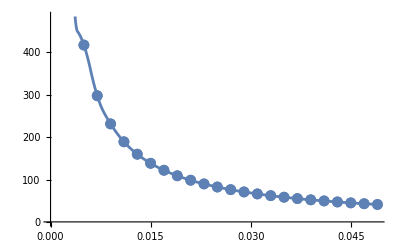

```mathematica
f=Interpolation[crossSections,InterpolationOrder->2];

Plot[f[x],{x,crossSections[[1,1]],crossSections[[11,1]]},Epilog->Point[crossSections],AxesLabel->{x,y}]
```

```mathematica
({{0.001, 2091.2221295028357}, {0.003, 696.3255239517729}, {0.005, 417.345553649013}, {0.007, 297.7784743840605}, {0.009000000000000001, 231.34359788520266}, {0.011, 189.05886709504892}, {0.013000000000000001, 159.7752657201317}, {0.015, 138.29131530922}, {0.017, 121.85320331743206}, {0.019000000000000003, 108.8672167473114}, {0.021, 98.34699558829088}, {0.023, 89.6495420941042}, {0.025, 82.33781080212431}, {0.027000000000000003, 76.10461626832144}, {0.029, 70.72744976885737}, {0.031, 66.04159090704565}, {0.033, 61.92224165642259}, {0.035, 58.272861074574294}, {0.037000000000000005, 55.01880824830472}, {0.039, 52.09945079272499}, {0.041, 49.466798571871195}, {0.043000000000000003, 47.08133910194116}, {0.045, 44.91080440039996}, {0.047, 42.927884785375745}, {0.049, 41.110013288574244}})

Plot[Interpolation[crossSections[[1]],crossSections[[2]]]]
```

{{0.001,2091.22},{0.003,696.326},{0.005,417.346},{0.007,297.778},{0.009,231.344},{0.011,189.059},{0.013,159.775},{0.015,138.291},{0.017,121.853},{0.019,108.867},{0.021,98.347},{0.023,89.6495},{0.025,82.3378},{0.027,76.1046},{0.029,70.7274},{0.031,66.0416},{0.033,61.9222},{0.035,58.2729},{0.037,55.0188},{0.039,52.0995},{0.041,49.4668},{0.043,47.0813},{0.045,44.9108},{0.047,42.9279},{0.049,41.11}}

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Interpolation[crossSections⟦1⟧,crossSections⟦2⟧]]